# Cosmomathica v1.0

Santiago Casas, 2018

This notebook demonstrates how to use the Cosmomathica package version 1.0

## Calling external programs

### Initialization

First, load the Cosmomathica package

```mathematica
NotebookDirectory[]
```

/local/home/scasas/CosmoProjects/cosmomathica/

```mathematica
<<(NotebookDirectory[]<>"cosmomathica.m")
```

### CAMB

CAMB takes a lot of parameters. In Cosmomathica, most of them are being treated as options with default values while some of them are regular parameters that have to be specified. The distinction is arbitrary. These are the default options (see the CAMB documentation for details):

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, h] :
provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
Options[CAMB]
```

{MGflag→0,pureMGflag→1,altMGflag→1,QSAflag→1,mugammapar→2,musigmapar→1,QRpar→1,DEmodel→1,GRtrans→0.001,B1→0.,lambda12→0.,B2→0.,lambda22→0.,ss→4.,E11→0.,E22→0.,mu0→-1.,sigma0→0.,MGQfix→0.,MGRfix→0.,Qnot→1.,Rnot→1.,sss→0.,Lindergamma→0.545,betastar→0.,astar→0.5,xistar→0.001,beta0→1.,xi0→0.0001,DilS→0.24,DilR→1.,FR0→0.0001,FRn→1.,w0ppf→-1.,wappf→0.,Tcmb→2.7255,OmegaNu→0,OmegaK0→0.,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→pk,HalofitVersion→4,WantCMB→True,WantTransfer→True,WantCls→False,WantScalars→False,WantVectors→False,WantTensors→False,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,AccuracyBoost→2,TransferHighPrecision→True,TransferInterpMatterPower→False,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→4000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→5,TransferKperLogInt→50,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→False,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best,debugIntFloats→False}

```mathematica
?MGflag
```

An option for CAMB/MGCAMB: 
          MG_flag = 0 :  default GR
          MG_flag = 1 :  pure MG models
          MG_flag = 2 :  alternative MG models
          MG_flag = 3 :  QSA models

```mathematica
?QSAflag
```

An option for CAMB/MGCAMB: 
QSA_flag = 1 : f(R)
QSA_flag = 2 : Symmetron      
QSA_flag = 3 : Dilaton
QSA_flag = 4 : Hu-Sawicki f(R)

```mathematica
?FR0
```

Parameter options for MGCAMB

```mathematica
?MasslessNeutrinos
```

An option for CAMB

```mathematica
?HalofitVersion
```

An option for CAMB. Integer number that chooses the Halofit version used in the non-linear matter power spectrum.
1: Original, 2: Bird, 3: Peacock, 4: Takahashi, 5: Mead, 6: Halo model, 7: Casarini,
8: Mead2015, 9: Winther-f(R)

Default values of some CAMB default options:

```mathematica
OptionValue[CAMB,#]&/@{MGflag,FR0,FRn, OmegaNu,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions,ScalarSpectralIndex,ScalarPowerAmplitude,MaxEtaK,TransferKmax, HalofitVersion}
```

{0,0.0001,1.,0,3.046,{0},{1},{0.96},{2.1×10^-9},4000.,5,4}

Run the CAMB code (without lensing the scalar angular power spectrum will contain only three curves corresponding to C_TT, C_EE, C_TE - see the CAMB documentation for further information) with the transfer function for two different redshifts

```mathematica
Interrupt[]
```

$Aborted

```mathematica
cambdata[0]=CAMB[0.25,0.05,0.67,TransferRedshifts->{1.5,0.}, WantCls->True,WantScalars->True, HalofitVersion->4, MGflag->0, QSAflag->4, FR0->10^(-4), FRn->1]
```

{CAMB[age]→14.0639,CAMB[zstar]→19,12,1,CAMB[Transfer]→{{{5.14524×10^-6,1.03905×10^7,1.03905×10^7,1.38532×10^7,1.38532×10^7,0.,1.03905×10^7,1.03905×10^7,1.04013×10^7,-0.584972,9.62766×10^6,9.62766×10^6,4.9902},361,{5.06605,2809.73,2781.67,0.0000176816,0.0000158539,0.,2805.05,2805.05,2805.05,-0.000157617,2598.54,2597.36,0.000071772}},{1}}}
 |  |  |  |

```mathematica
cambdata[4]=CAMB[0.25,0.05,0.67,TransferRedshifts->{1.5,0.}, WantCls->True,WantScalars->True, HalofitVersion->4, MGflag->3, QSAflag->4, FR0->10^(-4), FRn->1]
```

{CAMB[age]→14.0639,14,CAMB[Transfer]→{{{5.14524×10^-6,1.03905×10^7,1.03905×10^7,1.38532×10^7,1.38532×10^7,0.,1.03905×10^7,1.03905×10^7,1.04013×10^7,-0.584972,9.62766×10^6,9.62766×10^6,4.9902},361,{5.06605,7019.67,6991.21,0.00019831,0.0000456178,0.,7014.93,7014.93,7014.93,-0.00039417,12262.8,12260.9,0.000114755}},{{1},361,{1}}}}
 |  |  |  |

```mathematica
Do[
If[ii==0,mm=0,mm=3];
Print["ii:", ii];
cambdata[ii]=CAMB[0.25,0.05,0.67,TransferRedshifts->{1.5,0.}, WantCls->True,WantScalars->True, HalofitVersion->9, MGflag->mm, QSAflag->4, FR0->10^(-ii), FRn->1];
,{ii,{0,4,5,6}}]
```

ii:0

ii:4

ii:5

ii:6

```mathematica
(*cambdata6HaloWin=CAMB[0.25,0.05,0.67,TransferRedshifts->{1.5,0.}, WantCls->True,WantScalars->True, MGflag->3, QSAflag->4, FR0->10^(-6), FRn->1, HalofitVersion->9];*)
```

```mathematica
redz=2;
```

```mathematica
Do[
Print["ii:", ii];
kvals[ii]=((CAMB["PSlinear"]/.cambdata[ii])[[redz]])[[All,1]];
psl[ii]=((CAMB["PSlinear"]/.cambdata[ii])[[redz]])[[All,2]];
psnl[ii]=((CAMB["PSnonlinear"]/.cambdata[ii])[[redz]])[[All,2]];
tr[ii]=((CAMB["Transfer"]/.cambdata[ii])[[redz]])[[All,2]];
ratioLin[ii]=psl[ii]/psl[0];
ratioNonLin[ii]=psnl[ii]/psnl[0];
,{ii,{0,4}}]
```

ii:0

ii:4

```mathematica
cambdata[0][[All,1]]
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[sigma8],CAMB[CLscalar],CAMB[redshifts],CAMB[PSlinear],CAMB[PSnonlinear],CAMB[Transfer]}

Age of the universe:

```mathematica
CAMB["age"]/.cambdata[0]
```

14.0639

There is a σ_8 for each redshift and for each spectral index

```mathematica
CAMB["sigma8"]/.cambdata[0]
```

{{0.393337},{0.785823}}

```mathematica
CAMB["sigma8"]/.cambdata[4]
```

{{0.421716},{1.43167}}

Plot the scalar angular power spectrum for TT

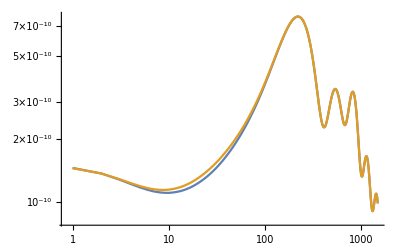

```mathematica
ListLogLogPlot[{(CAMB["CLscalar"]/.cambdata[0])[[1]],(CAMB["CLscalar"]/.cambdata[4])[[1]]} ,Joined->True]
```

Plot the scalar angular power spectrum for EE and TE

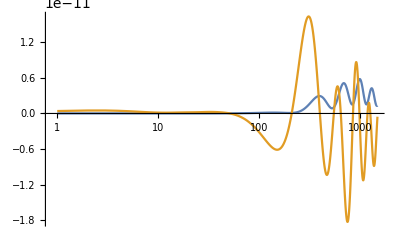

```mathematica
ListLogLinearPlot[(CAMB["CLscalar"]/.cambdata[0])[[2;;3]],Joined->True]
```

The results for the linear/nonlinear power spectrum as well as the transfer function contain a list for each redshift. Each one of those is a list of number pairs {k_i,P(k_i)} in the case of the power spectrum, and a list of seven numbers {k_i,T_1(k_i),..., T_6(k_i)} in case of the transfer function, each of which correspond to CDM, baryon, photon, massless neutrino, massive neutrinos, and total (massive).

Plot the nonlinear matter power spectrum for all redshifts

```mathematica
CAMB["redshifts"]/.cambdata[0]
```

{1.5,0.}

```mathematica
(*raplo=ListLogLinearPlot[{ratio4, ratio5,  ratio6, ratio1},Joined->True (*PlotLegends->Placed[LineLegend[{"logfR0=-4,","logfR0=-5", "logfR0=-6", "LCDM"}], Scaled[{0.1,0.8}]]*), PlotStyle->Thick, Frame->True, FrameLabel->{"", Style["P_fR(k)/P_LCDM(k)", Bold, 10]} , ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10]]*)
```

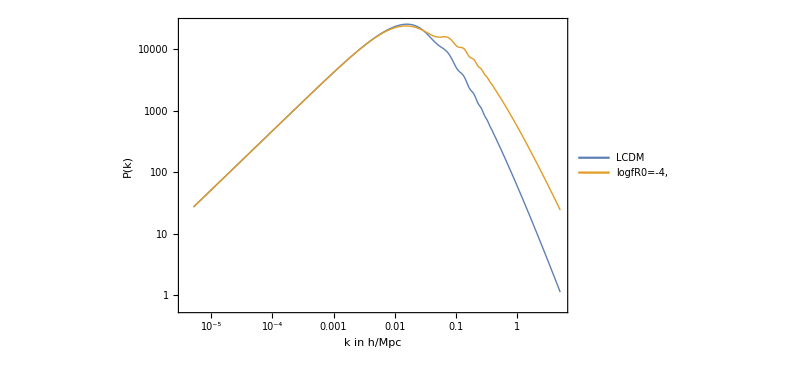

```mathematica
ListLogLogPlot[Evaluate@((Thread[{kvals[#],psnl[#]}]&/@{0,4})),Joined->True, PlotLegends->Placed[LineLegend[{"LCDM","logfR0=-4,","logfR0=-5","logfR0=-6"}], Scaled[{0.2,0.8}]], PlotStyle->Thick, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16](*Epilog->Inset[raplo, Scaled[{0.5,0.3}]]*)]
```